```mathematica
Clear[w0u,w1d,w1u,w0d,daprox]
```

```mathematica
daprox
```

daprox

```mathematica
aa0=2/3 x0;aa1=3x0/2;bb0=(4x0+1)/3;bb1=(3x0-1)/4; cc0=(4x0-1)/3;cc1=(3x0+1)/4;
aa0i=(2/3)^i x0;aa1i=(3/2)^i x0;bb0i=(-1+Factor[(4/3)^i+(4/3)^i x0])/.i->j; bb1i=(-1+Factor[(3/4)^i+(3/4)^i x0])/.i->j;cc0i=(1+Factor[-(4/3)^i+(4/3)^i x0])/.i->k;cc1i=1+Factor[-(3/4)^i+(3/4)^i x0]/.i->k;
```

```mathematica
w0u=2^d(2/3)^n x0+(4/3)^d-1; w0d=2^d(2/3)^n x0-(4/3)^d+1;
```

```mathematica
w1u=(3/2)^(n-d) (1-(3/4)^d+(3/4)^d x0);w1d=(3/2)^(n-d) (-1+(3/4)^d+(3/4)^d x0);
```

```mathematica
{w0u-w1d,w1u-w0d}
```

{-1+(4/3)^d+2^(d+n) 3^-n x0-(2/3)^(d-n) (-1+(3/4)^d+(3/4)^d x0),-1+(4/3)^d-2^(d+n) 3^-n x0+(3/2)^(-d+n) (1-(3/4)^d+(3/4)^d x0)}

```mathematica
%125/.i->n-d
```

%125

```mathematica
Factor[%78]
```

%78

```mathematica
{ (2^(2 d) 3^n-3^(d+n)+2^(d+n) 3^d x0-3^(d+n) x0), (2^(3 d+n) 3^n-3^(d+2 n)-6^(d+n)+2^(2 d) 9^n-2^(2 d+2 n) 3^d x0+3^(d+2 n) x0)}
```

{2^(2 d) 3^n-3^(d+n)+2^(d+n) 3^d x0-3^(d+n) x0,2^(3 d+n) 3^n-3^(d+2 n)-6^(d+n)+2^(2 d) 9^n-2^(2 d+2 n) 3^d x0+3^(d+2 n) x0}

```mathematica
{Factor[2^(2 d) 3^n-3^(d+n)]+Factor[2^(d+n) 3^d x0-3^(d+n) x0],2^(3 d+n) 3^n-3^(d+2 n)-6^(d+n)+2^(2 d) 9^n-2^(2 d+2 n) 3^d x0+3^(d+2 n) x0}
```

{3^n (2^(2 d)-3^d)+3^d (2^(d+n)-3^n) x0,2^(3 d+n) 3^n-3^(d+2 n)-6^(d+n)+2^(2 d) 9^n-2^(2 d+2 n) 3^d x0+3^(d+2 n) x0}

```mathematica
{3^n (2^(2 d)-3^d)+3^d (2^(d+n)-3^n) x0,Factor[2^(3 d+n) 3^n-3^(d+2 n)-6^(d+n)+2^(2 d) 9^n]-2^(2 d+2 n) 3^d x0+3^(d+2 n) x0}
```

{3^n (2^(2 d)-3^d)+3^d (2^(d+n)-3^n) x0,3^n (2^(2 d)-3^d) (2^(d+n)+3^n)-2^(2 d+2 n) 3^d x0+3^(d+2 n) x0}

```mathematica
{3^n (2^(2 d)-3^d)+3^d (2^(d+n)-3^n) x0,3^n (2^(2 d)-3^d) (2^(d+n)+3^n)+Factor[-2^(2 d+2 n) 3^d x0+3^(d+2 n) x0]}
```

{3^n (2^(2 d)-3^d)+3^d (2^(d+n)-3^n) x0,3^n (2^(2 d)-3^d) (2^(d+n)+3^n)-3^d (2^(d+n)-3^n) (2^(d+n)+3^n) x0}

```mathematica
{3^n (2^(2 d)-3^d)+3^d (2^(d+n)-3^n) x0,Factor[3^n (2^(2 d)-3^d) (2^(d+n)+3^n)-3^d (2^(d+n)-3^n) (2^(d+n)+3^n) x0]}
```

{3^n (2^(2 d)-3^d)+3^d (2^(d+n)-3^n) x0,(2^(d+n)+3^n) (2^(2 d) 3^n-3^(d+n)-2^(d+n) 3^d x0+3^(d+n) x0)}

```mathematica
{3^n (2^(2 d)-3^d)+3^d (2^(d+n)-3^n) x0,(2^(2 d) 3^n-3^(d+n)-2^(d+n) 3^d x0+3^(d+n) x0)}
```

{3^n (2^(2 d)-3^d)+3^d (2^(d+n)-3^n) x0,2^(2 d) 3^n-3^(d+n)-2^(d+n) 3^d x0+3^(d+n) x0}

```mathematica
{3^n (2^(2 d)-3^d)+3^d (2^(d+n)-3^n) x0,Factor[2^(2 d) 3^n-3^(d+n)]+Factor[-2^(d+n) 3^d x0+3^(d+n) x0]}
```

{3^n (2^(2 d)-3^d)+3^d (2^(d+n)-3^n) x0,3^n (2^(2 d)-3^d)-3^d (2^(d+n)-3^n) x0}

```mathematica
{3^(n-d) (2^(2 d)-3^d)+ (2^(d+n)-3^n) x0,3^(n-d) (2^(2 d)-3^d)- (2^(d+n)-3^n) x0}
```

{3^(-d+n) (2^(2 d)-3^d)+(2^(d+n)-3^n) x0,3^(-d+n) (2^(2 d)-3^d)-(2^(d+n)-3^n) x0}

```mathematica
(*Boundings for x0*)
```

```mathematica
www={3^(-d+n) (-3^d+4^d)+(2^(d+n)-3^n) x0,3^(-d+n) (-3^d+4^d)-(2^(d+n)-3^n) x0}
```

{3^(-d+n) (-3^d+4^d)+(2^(d+n)-3^n) x0,3^(-d+n) (-3^d+4^d)-(2^(d+n)-3^n) x0}

```mathematica
%/.n->10
```

{3^(10-d) (-3^d+4^d)+(-59049+2^(10+d)) x0,3^(10-d) (-3^d+4^d)-(-59049+2^(10+d)) x0}

```mathematica
wwwu[n_,d_]:=3^(-d+n) (-3^d+4^d)+((2^(d+n)-3^n)x0);
```

```mathematica
wwwd[n_,d_]:=3^(-d+n) (-3^d+4^d)-((2^(d+n)-3^n) x0);
a[n_,d_]:=3^(-d+n) (-3^d+4^d);
```

```mathematica
b[n_,d_]:=(2^(d+n)-3^n);
```

```mathematica
valuesx[n_,d_]:=Abs[N[a[n,d]/b[n,d]]];
```

```mathematica
valuesx[20,daprox[20]]
```

ⅇ^(1.09861 (20.-1. Re[daprox[20.]])) Abs[(-1. 3.^daprox[20.]+4.^daprox[20.])/(-3.48678×10^9+2.^(20.+daprox[20.]))]

```mathematica
3^(-d+n) (2^(2 d)-3^d)/2^n/c^n
```

2^-n 3^(-d+n) (2^(2 d)-3^d) c^-n

```mathematica
%68/.(2^(2d))->4^d
```

%68

```mathematica
%
```

%68

```mathematica
2^-n 3^(-d+n) (4^d) c^-n
```

2^(2 d-n) 3^(-d+n) c^-n

```mathematica
daprox[n_]:=Round[n Log[2,3/2]];
```

```mathematica
%73/.d->%
```

%73

```mathematica
FullSimplify[%]
```

%73

```mathematica
%/.n->1
```

%73

```mathematica
3^(Log[16/3]/Log[2])/(8 c)/.c->0.58
```

3.06019

```mathematica
a1=Table[N[Solve[wwwu[n,daprox[n]]==0,x0]],{n,20}];
```

```mathematica
N[Solve[wwwu[20,daprox[20]]==0,x0]]
```

{{x0→-131.887}}

```mathematica
wwwu[306,daprox[306]]
```

2307479211631865702655700223555493692142354104042678711547189796880677125370567257359377377469353015847855132522409096285330335343248562191069323386605143508647660652599+102065376400825306534437391838939444403106454408085639783964140880896699835673006969445010534504805079858638689074275443284439551032910142670903 x0

```mathematica
Solve[N[2307479211631865702655700223555493692142354104042678711547189796880677125370567257359377377469353015847855132522409096285330335343248562191069323386605143508647660652599+102065376400825306534437391838939444403106454408085639783964140880896699835673006969445010534504805079858638689074275443284439551032910142670903 x0]==0,x0]
```

{{x0→-2.26079×10^25}}

```mathematica
a2=Table[N[Solve[wwwd[n,daprox[n]]==0,x0]],{n,120}]
```

{{{x0→1.}},{{x0→-3.}},{{x0→4.2}},{{x0→-3.70588}},{{x0→25.6154}},{{x0→5.33898}},{{x0→-33.9928}},{{x0→12.9289}},{{x0→-19.1758}},{{x0→42.0421}},{{x0→-17.7576}},{{x0→-482.297}},{{x0→28.5006}},{{x0→-73.0344}},{{x0→72.789}},{{x0→-55.8624}},{{x0→426.207}},{{x0→58.7855}},{{x0→-297.748}},{{x0→131.887}},{{x0→-170.959}},{{x0→432.918}},{{x0→-152.164}},{{x0→-2061.6}},{{x0→248.019}},{{x0→-547.389}},{{x0→643.501}},{{x0→-427.59}},{{x0→5212.63}},{{x0→480.453}},{{x0→-1990.8}},{{x0→1094.32}},{{x0→-1240.38}},{{x0→3920.27}},{{x0→-1123.12}},{{x0→-10528.9}},{{x0→1997.03}},{{x0→-3819.2}},{{x0→5410.35}},{{x0→-3092.83}},{{x0→86359.}},{{x0→3807.88}},{{x0→-13164.6}},{{x0→8905.09}},{{x0→-8820.01}},{{x0→35972.4}},{{x0→-8154.68}},{{x0→-59680.4}},{{x0→15965.7}},{{x0→-26572.7}},{{x0→45646.3}},{{x0→-22255.4}},{{x0→-3.5788×10^6}},{{x0→30113.1}},{{x0→-88115.2}},{{x0→72640.1}},{{x0→-62745.8}},{{x0→344962.}},{{x0→58735.3}},{{x0→-360184.}},{{x0→127900.}},{{x0→-185786.}},{{x0→390069.}},{{x0→-160333.}},{{x0→-3.60448×10^6}},{{x0→238537.}},{{x0→-597072.}},{{x0→596162.}},{{x0→-447635.}},{{x0→3.56881×10^6}},{{x0→461718.}},{{x0→-2.26379×10^6}},{{x0→1.0283×10^6}},{{x0→-1.30566×10^6}},{{x0→3.39254×10^6}},{{x0→-1.15721×10^6}},{{x0→-1.45656×10^7}},{{x0→1.89407×10^6}},{{x0→-4.08759×10^6}},{{x0→4.93044×10^6}},{{x0→-3.20256×10^6}},{{x0→4.28299×10^7}},{{x0→3.63574×10^6}},{{x0→-1.4634×10^7}},{{x0→8.3029×10^6}},{{x0→-9.21823×10^6}},{{x0→3.02117×10^7}},{{x0→-8.36722×10^6}},{{x0→-7.50266×10^7}},{{x0→1.50806×10^7}},{{x0→-2.8223×10^7}},{{x0→4.1157×10^7}},{{x0→-2.29721×10^7}},{{x0→7.9001×10^8}},{{x0→2.86833×10^7}},{{x0→-9.65683×10^7}},{{x0→6.73722×10^7}},{{x0→-6.53467×10^7}},{{x0→2.78109×10^8}},{{x0→-6.06003×10^7}},{{x0→-4.29638×10^8}},{{x0→1.20439×10^8}},{{x0→-1.96263×10^8}},{{x0→3.47501×10^8}},{{x0→-1.65168×10^8}},{{x0→-1.33758×10^10}},{{x0→2.26758×10^8}},{{x0→-6.4735×10^8}},{{x0→5.49812×10^8}},{{x0→-4.64894×10^8}},{{x0→2.69073×10^9}},{{x0→4.41764×10^8}},{{x0→-2.61162×10^9}},{{x0→9.65159×10^8}},{{x0→-1.37312×10^9}},{{x0→2.97635×10^9}},{{x0→-1.1901×10^9}},{{x0→-2.3767×10^10}},{{x0→1.79673×10^9}},{{x0→-4.39372×10^9}}}

```mathematica
wwwu[20,daprox[20]]
```

106588529775+808182895 x0

```mathematica
wwwd[20,daprox[20]]
```

106588529775-808182895 x0

```mathematica
Solve[106588529775-808182895 x0==0,x0]S
```

{{S (x0→1639823535/12433583)}}

```mathematica
N[{{x0->1639823535/12433583}}]
```

{{x0→131.887}}

```mathematica
(*Listplot of lenghts and starting points*)
```

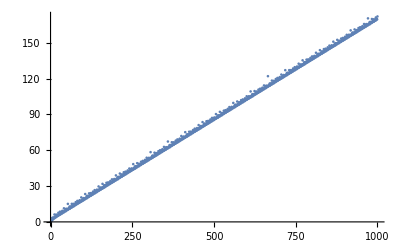

```mathematica
ListPlot[Log[Table[valuesx[n,daprox[n]],{n,1,1000}]]]
```

```mathematica
Show[%129,AxesLabel->{HoldForm[Cycle length],HoldForm[Maximum possible integer]},PlotLabel->HoldForm[Cycle' s Boundaries],LabelStyle->{GrayLevel[0]}]
```

Show::gtype: Out is not a type of graphics.

Show[%129,AxesLabel→{Cycle length,Maximum possible integer},PlotLabel→Cycle' s Boundaries,LabelStyle→{GrayLevel[0]}]

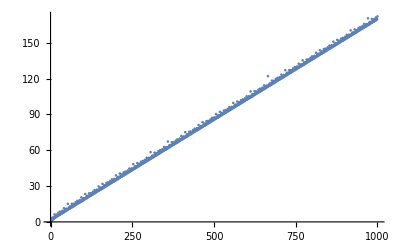

```mathematica
Show[ListPlot[Log[Table[valuesx[n,daprox[n]],{n,1,1000}]]],Plot[2.013881054483857+0.1683539045172308 x,{x,0,1000}]]
```

```mathematica
Show[%38,AxesLabel->{HoldForm[Cycle length],HoldForm[Log (maximal Integer)]},PlotLabel->HoldForm[Cycles Boundaries],LabelStyle->{GrayLevel[0]}]
```

Show::gtype: Out is not a type of graphics.

Show[%73,AxesLabel→{Cycle length,Log (maximal Integer)},PlotLabel→Cycles Boundaries,LabelStyle→{GrayLevel[0]}]

```mathematica
Show[%139,AxesLabel->{HoldForm[Cycle length],HoldForm[Log[maximal Integer]]},PlotLabel->HoldForm[Line of best fit for cycle' s boundaries],LabelStyle->{GrayLevel[0]}]
```

Show::gtype: Out is not a type of graphics.

Show[%139,AxesLabel→{Cycle length,Log[maximal Integer]},PlotLabel→Line of best fit for cycle' s boundaries,LabelStyle→{GrayLevel[0]}]